```mathematica
c := 3*10^(10) 
G:= 6.67*10^(-8)
hbar := 1.054*10^(-27) (* cte de plack reducida*)
kb := 1.3806*10^(-16) (* cte de boltzmann*)
```

```mathematica
gstar := 10.75 (* grados de libertad*)
TBBN := (10^6*1.6*10^(-12))/kb  (* temperatura en BBN [K]*)
```

```mathematica
ρradBBN = π^2/30*gstar*(kb^4*TBBN^4)/(hbar*c)^3
```

7.33131×10^26

```mathematica
β := 10^(-8)
ρ0 =β*ρradBBN
```

7.33131×10^18

```mathematica
ati := 1.66*10^(-10)
ti := 0.74 (*s*)
n:=1
k = (4π *G)/(3*c^2)*ρ0 *(ati)^(3-n)
Hti = √((8π G)/(3c^2)(ρradBBN + ρ0))
Dati := Hti * ati (* 1/s*)
```

6.27147×10^-29

0.67467

```mathematica
A := 2ati^2*Hti -2k ti
B := ati^2 +k *ti-2ati^2*Hti*ti
```

```mathematica
a1[t_]:= √(k t^2+A t+B)
```

```mathematica
ρbh[t_]:= ρbh0*(ati/a1[t])^2
```

```mathematica
Da[t_]:=(A+2 k t)/(2 √(B+A t+k t^2))
ρcf[t_]:= (3c^2)/(8π G)(Da[t]/a1[t])^2-ρ0 (ati/a1[t])^(3-n)
```

```mathematica
cociente[t_]:= ρbh[t]/(ρbh[t]+ρcf[t])
```

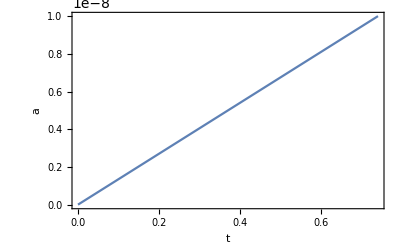

```mathematica
Plot[cociente[t], {t, 10^(-4), ti}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

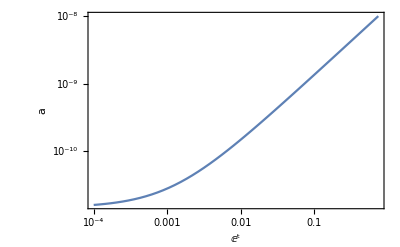

```mathematica
LogLogPlot[cociente[t], {t, 10^(-4), ti}, AxesLabel->{t,a},Frame->True, PlotRangePadding->0 ]
```

```mathematica
βobs := β/(β+1)
```

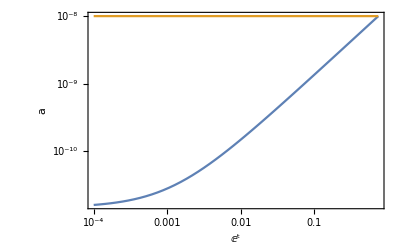

```mathematica
LogLogPlot[{cociente[t], βobs}, {t, 10^(-4), ti}, AxesLabel->{t,a},Frame->True ]
```

```mathematica
Clear[n]
```